## Mixture models for the step-length distribution: model evaluation

Choose number of components based on AIC and ancillary criteria.

```mathematica
Remove["Global`*"]
```

Models specifications (one, two and three components, see Ly et al. equation 4).

```mathematica
d1=RayleighDistribution[s3 ];
d2=MixtureDistribution[{p2,1-p2},{RayleighDistribution[s2 ],RayleighDistribution[s3 ]}];
d3=MixtureDistribution[{p1,p2,1-p2-p1},{RayleighDistribution[s1 ],RayleighDistribution[s2 ],RayleighDistribution[s3 ]}];
d4=MixtureDistribution[{p1,p2,p3,1-p2-p1-p3},{RayleighDistribution[s1 ],RayleighDistribution[s2 ],RayleighDistribution[s3 ],RayleighDistribution[s4]}];
```

Set working directory to the location of the data files

```mathematica
SetDirectory["/Users/jfreites/OneDriveUCIrvine/Code/Piezo1-tdTomato-Trajectory-Analysis/examples/untreated/"];
```

```mathematica
filenames=Flatten[Import["../260_jsons/260_untreated/260_untreatedJson","Data"]];
```

Base filename for output

```mathematica
myOutName="260_untreated_d1throughd3_results_";
```

These are the actual step-length data as a single table

```mathematica
datas=Table[Import[filenames[[i]]<>"-StepLengthDelta-1-200.dat"],
{i,1,Length@filenames}];
data2=Flatten[datas,1];
data2=DeleteCases[data2,$Failed];
Length@data2
```

1861

MLE results and assessments:

```mathematica
results=Get["260_untreated_assessment_res_d3"];
results=DeleteCases[results,{}];
```

The results object is a list with one element per JSON array from a single experimental session:

```mathematica
Head@results
```

List

```mathematica
Dimensions@results
```

{19}

Each sublist has an entry for each trajectory in the form of a 3-by-3 table with the results from the three models for each particular trajectory:

```mathematica
Dimensions@results[[1]]
```

{61,3,3}

```mathematica
results[[1]][[1]]
```

{{1.45988×10^-6,{s3→0.470626},-168.27},{0.336573,{p2→0.858965,s2→0.381672,s3→0.826582},-127.912},{0.962058,{p1→0.362929,p2→0.606221,s1→0.281693,s2→0.495365,s3→1.19332},-123.485}}

The models are organized by row (first row, single component model; second, 2-component mixture model; third, 3-component mixture model).  First column are the p-values from the Anderson-Darling test. The second column are the model parameters (p: mixing proportions; s: sigma values; see Ly et al. eq 4). The third column are log-likelihood values:

```mathematica
results[[1]][[1]]//Grid
```

1.45988×10^-6 | {s3→0.470626} | -168.27
0.336573 | {p2→0.858965,s2→0.381672,s3→0.826582} | -127.912
0.962058 | {p1→0.362929,p2→0.606221,s1→0.281693,s2→0.495365,s3→1.19332} | -123.485

These are “extractor” function for the model parameters and p-values matching the structure of the results object:

```mathematica
getPvals[n_,res_]:=Flatten@Table[res[[i]][[All,n,1]],{i,Length@res}]
getParams[n_,plist_,res_]:=Flatten[Table[plist/.res[[i]][[All,n,2]],{i,Length@results}],1]
```

```mathematica
(* make sure that the parameter labels are correct *)
params1c=getParams[1,s3,results];
params2c=getParams[2,{p2,s2,s3},results];
params3c=getParams[3,{p1,p2,s1,s2,s3},results];
(*params4c=getParams[4,{p1,p2,p3,s1,s2,s3,s4},results];*)
```

```mathematica
pvals1c=getPvals[1,results];
pvals2c=getPvals[2,results];
pvals3c=getPvals[3,results];
(*pvals4c=getPvals[4,results];*)
```

Specific trajectory models, input are parameters:

```mathematica
myModel1[s_]:=d1/.s3->s
myModel2[lista_]:=d2/.{p2->lista[[1]],s2->lista[[2]],s3->lista[[3]]}
myModel3[lista_]:=d3/.{p1->lista[[1]],p2->lista[[2]],s1->lista[[3]],s2->lista[[4]],s3->lista[[5]]}
myModel4[lista_]:=d4/.{p1->lista[[1]],p2->lista[[2]],p3->lista[[3]],s1->lista[[4]],s2->lista[[5]],s3->lista[[6]],s4->lista[[7]]}
```

Useful plotting functions:

```mathematica
plotMyModels[n_]:=Show[Histogram[data2⟦n⟧,"FreedmanDiaconis","PDF"],
Plot[PDF[myModel4[params4c⟦n⟧],x],{x,0,4},PlotRange->Full,PlotStyle->Purple],
Plot[PDF[myModel3[params3c⟦n⟧],x],{x,0,4},PlotRange->Full,PlotStyle->Blue],Plot[PDF[myModel2[params2c⟦n⟧],x],{x,0,4},PlotRange->Full,PlotStyle->Cyan],Plot[PDF[myModel1[params1c⟦n⟧],x],{x,0,4},PlotRange->Full,PlotStyle->Red]]
```

```mathematica
plotMyComponents[n_]:=Show[Histogram[data2⟦n⟧,"FreedmanDiaconis","PDF"],Plot[PDF[myModel2[params2c⟦n⟧],x],{x,0,4},PlotRange->Full,PlotStyle->Cyan],Plot[params2c⟦n⟧[[1]]*PDF[myModel1[params2c⟦n⟧[[2]]],x],{x,0,4},PlotRange->Full,PlotStyle->Magenta],
Plot[(1-params2c⟦n⟧[[1]])*PDF[myModel1[params2c⟦n⟧[[3]]],x],{x,0,4},PlotRange->Full,PlotStyle->Green]]
```

### Overall number of components selection scheme

Identify non-converged across all models (via dummy answers from Check)

Identify “bad” goodness-of-fit across all models  (e.g. via all pvals < =0.05 or pvals==1, the latter is a dummy answer from Check)

Identify duplicates via equal sigmas in the k-component models (k=2,3,...)

Remove duplicates

compute AIC between distinct models

#### we seek the most parsimonious model

If out of all the available models the ΔAIC=0 is the one with the least number of components TAKE IT

If the 1-component is no good, then use same criterion for multiple components: If out of all the available models the ΔAIC=0 is the one with the least multiple components TAKE IT

If out of all the available models the ΔAIC=0 is not the the one with the least number of components, assume very similar log-likelihoods. Thus, ΔAIC = AIC1-AIC2 ~ 2(k2-k1). Take the one with the least components, that is if k1>k2 take the second  if AIC1-AIC2 < k1-k2

all sigmas and mixed sigmas:

```mathematica
allsigmas=Table[{params1c[[i]],params2c[[i,2;;3]],params3c[[i,3;;5]]}//Flatten,{i,Length@data2}];
mixsigmas=Table[{params2c[[i,2;;3]],params3c[[i,3;;5]]}//Flatten,{i,Length@data2}];
```

all pvals and all LLs

```mathematica
allpvals=Flatten[Table[results[[i]][[All,All,1]],{i,Length@results}],1];
```

```mathematica
allLL=Flatten[Table[results[[i]][[All,All,3]],{i,Length@results}],1];
```

#### Non-convergence across models

Overall non-convergence

```mathematica
noConverge=Position[ AllTrue[#*1. ,#==1.*^-9&]&/@allsigmas,True]//Flatten
```

{}

```mathematica
(*Table[plotMyModels[i],{i,noConverge//Flatten}]*)
```

No mixture model available

```mathematica
noMixture =Position[ AllTrue[#*1. ,#==1.*^-9&]&/@mixsigmas,True]//Flatten
```

{1370}

```mathematica
(*Table[plotMyModels[i],{i,noMixture//Flatten}]*)
```

#### No model is a good fit

No model describes the trajectory:

```mathematica
noModel=Position[AllTrue[(#<=0.05 || #==1)&]/@allpvals,True]//Flatten
```

{562,1069,1189,1232}

```mathematica
(*Table[plotMyModels[i],{i,noModel//Flatten}] *)
```

### Equal sigmas k-component

#### Equal sigmas 2-component

This  will include no-model by construction

```mathematica
equalSigma2c=Position[params2c,{x_,y_,z_}/;(Abs[y-z]<0.01)]
```

{{562},{771},{1189},{1217},{1370}}

Trajectories that can be described by a 2-component model (no duplicate parameters):

```mathematica
good2=Complement[Range[Length@data2],equalSigma2c//Flatten,noModel//Flatten];
```

#### Equal sigmas 3-component

```mathematica
equalSigma3c=Position[params3c,{p1_,p2_,s1_,s2_,s3_}/;(Abs[s1-s2]<0.01 || Abs[s1-s3]<0.01 || Abs[s3-s2]<0.01)];
equalSigma3c;
```

rajectories that can be described by a 3-component model (no duplicate parameters):

```mathematica
good3=Complement[Range[Length@data2],equalSigma3c//Flatten,noModel//Flatten];
```

#### Good 1-component model

```mathematica
good1=Complement[Range[Length@data2],noModel//Flatten,noConverge//Flatten];
```

### Gather all valid models and run AIC

At this point we have identified the duplicates in 3-component and 2-component models and should be eliminated as potential candidates

```mathematica
goodOnes={good1,good2,good3};
```

```mathematica
(*laVerdad=Table[MemberQ[#,i]&/@goodOnes,{i,Length@data2}]*)
```

```mathematica
(*MapAt[f,{a,b,c,d},{{1},{4}}]*)
```

```mathematica
(*ReplacePart[{a,b,c,d,e,f,g},{{1}}->xxx]*)
```

Compute  ΔAIC only on those models that are valid:

```mathematica
getDAIC[ll_,good_,k_:{1,3,5}]:=Module[{aic,daic},
aic=ReplacePart[2k-2ll,Position[good,False]->10^12];
daic=(#-Min[#])&@aic;
Return[daic];
]
```

```mathematica
deltaAIC=Table[getDAIC[allLL[[i]],MemberQ[#,i]&/@goodOnes,{1,3,5}],{i,Length@data2}];
```

```mathematica
(*and the corresponding weights:*)
(*akaikeW=(Exp[-0.5#]/Total[Exp[-0.5#]])&/@deltaAIC;*)
```

```mathematica
(*allLL[[noModel]]
deltaAIC[[noModel]]
PositionSmallest/@ % *)
```

### AIC analysis

#### Number of components in the top model

```mathematica
Tally[Position[#,0.]&/@deltaAIC]
(* check that everything is accounted for *)
Total[%[[All,2]]]==Length@data2
```

{{{{3}},409},{{{2}},1428},{{{1}},20},{{},4}}

True

#### 1-component work

All the models with a top 1-component includes trajectories with only a 1-component model as valid model and actual multiple-model with top 1 component

```mathematica
k11=Complement[Position[PositionSmallest/@deltaAIC,{1}]//Flatten,noModel,noConverge]
Length@k11
```

{122,147,322,609,679,771,802,891,1009,1071,1217,1221,1227,1292,1370,1410,1513,1559,1574,1627}

20

```mathematica
(*Table[plotMyModels[i],{i,RandomSample[los1,10]}]*)
```

#### 2-component top work

These are all the trajectory indices for which the top model is 2-component:

```mathematica
los2=                                                                                                                                                                                                                                           Position[PositionSmallest/@deltaAIC,{2}]//Flatten;
```

```mathematica
Length@los2
```

1428

We  are  only interested on those for which the second model is the 1-component and have a  ΔAIC < 4

```mathematica
(*This is how PositionSmallest[#,n] works,the first element is the smallest,the nth-element is the smallest*)
PositionSmallest[{4,2,1,2,5},3]
```

{{3},{2,4},{1}}

These are the trajectory indices for which the top model is 2-component and the second model is 1-component:

```mathematica
sel1from2=los2[[Position[PositionSmallest[#,2]&/@deltaAIC[[los2]],{{2},{1}}]//Flatten]];
```

```mathematica
Length@sel1from2
```

468

Out of those trajectories, which are the ones that have a ΔAIC < 4?

```mathematica
BinCounts[deltaAIC[[sel1from2]][[All,1]],{{0,4,Infinity}}]
```

{30,438}

These are the 1-component coming from 2-component top

```mathematica
k12=sel1from2[[Position[deltaAIC[[sel1from2]][[All,1]],n_/;n<4]//Flatten]];
```

```mathematica
Length@k12
```

30

```mathematica
(*Table[plotMyModels[i],{i,RandomSample[k12,5]}];*)
```

2-component coming from 2-component top

```mathematica
k22=Complement[los2,k12,noConverge,noModel];
Length@k22
```

1398

#### 3-component top work

now  we do the same with 3-component, we take the simplest model: 
	3-comp if there isn’t a 2-comp or 1-comp or if the second is 2-comp and ΔAIC  > 4
	2-comp if it’s second and  ΔAIC < 4
	if the second is 1-comp check carefully, is the equal LLs assumption still valid?

All the trajectory indices for which 3-comp is top model:

```mathematica
los3=Position[PositionSmallest/@deltaAIC,{3}]//Flatten;
```

```mathematica
Length@los3
```

409

first  we look at 2-component as second model:

```mathematica
sel2from3=los3[[Position[PositionSmallest[#,2]&/@deltaAIC[[los3]],{{3},{2}}]//Flatten]];
```

the ΔAIC = 4 partition:

```mathematica
BinCounts[deltaAIC[[sel2from3]][[All,2]],{{0,4,Infinity}}]
```

{254,154}

These are the trajectory indices for which the 2-comp is preferred ΔAIC < 4

```mathematica
k23=sel2from3[[Position[deltaAIC[[sel2from3]][[All,2]],n_/;n<4]//Flatten]];
Length@k23
```

254

These are the trajectory indices for which 1-component is second, should be considered case-by-case:

```mathematica
sel1from3=los3[[Position[PositionSmallest[#,2]&/@deltaAIC[[los3]],{{3},{1}}]//Flatten]];
```

```mathematica
BinCounts[deltaAIC[[sel1from3]][[All,1]],{{0,4,Infinity}}]
```

{1,0}

```mathematica
k13=sel1from3[[Position[deltaAIC[[sel1from3]][[All,1]],n_/;n<4]//Flatten]];
k13
```

{1075}

These  are the remaining 3-comp indices:

```mathematica
k33=Complement[los3,k23,k13,noConverge,noMixture];
Length@k33
```

154

At this point is recommended to check results as needed using the plot functions above. We skip that here.

### SUMMARY

These are the trajectory indices for trajectories with no model, “1-component”, 2-component, and 3-component:

```mathematica
k0={noConverge,noModel}//Flatten;
k1={k11,k12,k13 }//Flatten;
k2={k22,k23 }//Flatten;
k3={k33 }//Flatten;
```

and these are the corresponding counts and proportions:

```mathematica
counts=Length/@{k0,k1,k2,k3}
100*counts/Total@counts//N
Total@counts==Length@data2
```

{4,51,1652,154}

{0.214938,2.74046,88.7695,8.27512}

True

#### Final Output

CSV  files: traj index | p1 | ... |pk | s1 | ... |sk|

1-component

```mathematica
inds=Sort@k1;
pars=params1c[[inds]];
res=Transpose[{inds,pars}];
Dimensions@res
Export[myOutName<>"k1.csv",res,"CSV"];
```

{51,2}

2-component

```mathematica
inds=Sort@k2;
p=params2c[[inds,1]];
pis=Transpose@{p,1-p};
sigmas=params2c[[inds,2;;3]];
ord=Ordering/@sigmas;
res=Table[{inds[[i]],pis[[i]][[ord[[i]]]],sigmas[[i]][[ord[[i]]]]}//Flatten,{i,Length@inds}];
Export[myOutName<>"k2.csv",res,"CSV"];
Dimensions@res
```

{1652,5}

3-component

```mathematica
inds=Sort@k3;
p13=params3c[[inds,1]];
p23=params3c[[inds,2]];
pis=Transpose@{p13,p23,1-p13-p23};
sigmas=params3c[[inds,3;;5]];
ord=Ordering/@sigmas;
res=Table[{inds[[i]],pis[[i]][[ord[[i]]]],sigmas[[i]][[ord[[i]]]]}//Flatten,{i,Length@inds}];
Export[myOutName<>"k3.csv",res,"CSV"];
Dimensions@res
```

{154,7}

Express sigmas as apparent diffusion coefficients:

```mathematica
sigma2D[x_,micronPerPix_:.1091,secondsPerFrame_:100*10^-3,dt_:1.]:=(x*micronPerPix)^2/(2*dt*secondsPerFrame)
```

Here’s a plot similar to Ly et al. Figures 4 and 6. A smooth density histogram of the proportion and sigma for one component:

```mathematica
(* this isn't needed, just want to check that we can read the CSV *)
par2=Import[myOutName<>"k2.csv","CSV"];
```

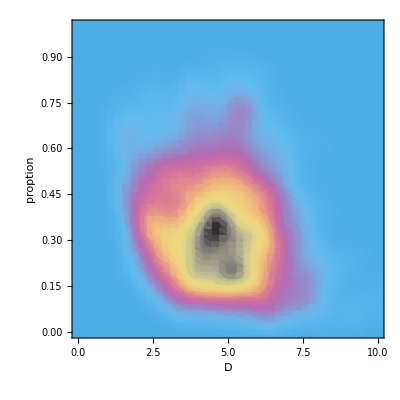

```mathematica
x=sigma2D/@par2[[All,5]];
y=par2[[All,3]];
SmoothDensityHistogram[{100x,y}//Transpose,Automatic,"Intensity",Mesh->10,MeshStyle->Thick,PlotRange->{{0,10},{0,1}},ColorFunction->"CMYKColors",FrameLabel->{"D","proption"}]
```